Koen Groenland, 2019

This is basically a modified version of the code  by StackOverflow user glS: https://mathematica.stackexchange.com/questions/125985/how-to-draw-an-interactive-mouse-clickable-3d-bloch-sphere. I changed it to create pretty black-and-white pictures that work well on printed paper. 

We require the package MaTeX for pretty typesetting, see https://github.com/szhorvat/MaTeX. If you insist on not using this package, you may freely change all MaTeX[..] commands into any other string.

## Figure of Bloch Sphere

#### Definitions: (collapsed by default)

```mathematica
Needs["MaTeX`"];

(* Define sharp circles to plot in 3D *)
splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3

(* Define pretty axis lines *)
pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points

(* Define the main circles of a sphere in 3D *)
surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

(* List of graphics primitives that constructs a pretty Bloch Sphere *)
BlochSphereGraphics = {
Black,
Opacity@1,Thickness@0.004,PointSize@0.02,
 pointsAndConnection@{{0,0,1},{0,0,-1}},
 pointsAndConnection@{{1,0,0},{-1,0,0}}, 
 pointsAndConnection@{{0,1,0},{0,-1,0}},
Black,Point[{0,0,0}],Text[ MaTeX["Z", Magnification->2.2 ],{0,0,1.1}],Text[ MaTeX["X", Magnification->2.2],{1.3,0,0}],Text[ MaTeX["Y", Magnification->2.2],{0,1.1,0}],
Gray,Thickness[0.001],surroundingCircles};

(* Options that make the Bloch Sphere graphics look good *)
BlochSphereOptionsYZ = {Boxed->False,PlotRange->ConstantArray[{-1.1,1.1},3],ImageSize->500,RotationAction->"Clip"
,ViewAngle -> 0.33,ViewPoint -> {3, .7, .9} ,ViewVertical -> {0, 0, 2} };

BlochSphereOptionsHex = {Boxed->False,PlotRange->ConstantArray[{-1.1,1.1},3],ImageSize->500,RotationAction->"Clip"
,ViewAngle -> 0.7,ViewPoint -> {1.5, .5, 1} ,ViewVertical -> {0, 0, 2} };

(* Plot a trajectory in 3D *)
TrajectorySettings =  { Gray, Opacity@1, Thickness@0.015  , Arrowheads[{0,0.0}]  };
TrajectoryFromFunction[ trajectoryFunction_, {tmin_, tmax_}, resolution_:100  ]:= GraphicsComplex[Table[trajectoryFunction[g],{g,Subdivide[tmin, tmax,resolution]}],Arrow[Range[resolution+1]]] ;

(* Allow one to solve time evolution *)
{X,Y,Z} = Table[ PauliMatrix[j], {j,3} ];

(* Solve time evolution starting in any state. The Hamiltonian may be a function of some parameter t. Returns a single InterpolatingFunction (that is vector-valued for each time t). Use a 2x2 Hamiltonian to get a result that plots on the Bloch Sphere.  *)
evolveState[ ham_, startstate_, {t_, tmin_, tmax_} ] := Module[ {sol, v}, 
  sol = NDSolve[ {I  v'[t] == ham . v[t], v[0] ==  startstate}, 
    v, {t, tmin, tmax} ] ;
  v  /. sol // Flatten // First
  ];

(* Maps the solution 'sol' of NDSolve (an InterpolatingFunction) at a given time t to a three-dimensional vector on the Bloch Sphere *)
evolutionFunctionToBlochVector[sol_, t_] := Table[ Re[ sol[t]* . op . sol[t] ], {op, {X,Y,Z} } ] ;

(* An all-in-one function that instantly plots the evolution *)
EvolutionOnBlochSphere[ Hamiltonian_, InitialState_,  {t_, tmin_,tmax_ }, Resolution_:100 ] := Module[{sol, blochcoords},
sol = evolveState[ Hamiltonian, InitialState, {t,tmin,tmax}];
blochcoords[g_] := evolutionFunctionToBlochVector[ sol, g ] ;
Return[ Graphics3D[ {
BlochSphereGraphics,
 Append[ TrajectorySettings,  TrajectoryFromFunction[ blochcoords, {tmin, tmax}, Resolution ] ]
}, BlochSphereOptionsYZ ]

];
];
```

#### Example usage:

Define a Hamiltonian, and some initial state (in 2 dimensions).

```mathematica
initialstate = {1,0};

ham = 8( Cos[ t ] Z - Sin[ t ] Y );
ham // MatrixForm
```

(8 Cos[t] | 8 ⅈ Sin[t]
-8 ⅈ Sin[t] | -8 Cos[t])

The simple method: Use the all-in-one function:

```mathematica
EvolutionOnBlochSphere[ ham ,initialstate,  {t,0,Pi } ]
```

-Graphics3D-

For more control, some steps can be done by hand. For example:

1. Solve the Hamiltonian

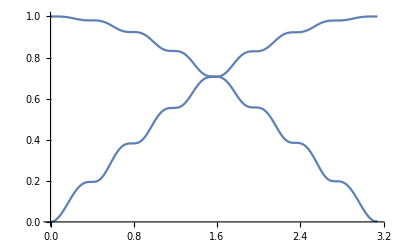

```mathematica
sol = evolveState[ ham, initialstate, {t,0,Pi}];
Plot[ Abs[sol[t] ], {t,0,Pi} ]
```

2. Map the time evolution to coordinates on the Bloch Sphere

```mathematica
blochcoords[t_] := evolutionFunctionToBlochVector[ sol, t ] 
blochcoords[0]
blochcoords[Pi]
```

{0.,0.,1.}

{-0.000299212,-0.00610812,-0.999983}

3. Create the Bloch Sphere using Graphics3D, and overlay the state’s evolution:

```mathematica
Graphics3D[ {
BlochSphereGraphics,
 Append[ TrajectorySettings,  TrajectoryFromFunction[ blochcoords, {0,Pi} ] ]
}, BlochSphereOptionsYZ ]
```

-Graphics3D-

#### Indicating a state

```mathematica
statelocation = Normalize[{1,2.3,2} ];
phi = ArcTan[ statelocation[[2]] / statelocation[[1]] ];
theta = ArcCos[ Abs[ statelocation[[3]] ] ];

thArcFun[x_] = .6 Normalize[ Cos[x/2] * {0,0,1} + Sin[x/2] statelocation ];
phiArcFun[x_] = .6 Normalize[ Cos[x/2] * {1,0,0} + Sin[x/2] statelocation*{1,1,0} ];

BlochWithState = Graphics3D[ {
BlochSphereGraphics

(* Indicating the state *)
,GrayLevel[0]
 ,Thickness[.008], Line[{{0,0,0},statelocation}], PointSize[0.02], Point[ statelocation ] 
,Text[MaTeX["\\lvert \\Psi \\rangle", Magnification->2], statelocation + {0,0,.1}]

(* Lines to state *)
, Thickness[0.004], Dashed,
, Line[{{0,0,0}, statelocation*{1,1,0}}] (* Bottom line *)
, Line[{ statelocation*{1,1,0}, statelocation*{1,1,1}}] (* Upward line *)

(* Angle circles *)
,Arrowheads[0],Thickness[0.002],Dashing[None],
,TrajectoryFromFunction[phiArcFun, {0,Pi}]
, TrajectoryFromFunction[ thArcFun, {0,Pi} ] 

,Text[MaTeX["\\theta", Magnification->2], statelocation * {.5,.4,1}]
,Text[MaTeX["\\phi", Magnification->2], statelocation * {1.5,.6,-0.1} ]

}, BlochSphereOptionsYZ ]
```

-Graphics3D-

```mathematica
Export["blochSphere.pdf",GraphicsRow[{BlochWithState},ImageSize->500]]
```

blochSphere.pdf

#### The X gate

```mathematica
xgatepath[x_] := {0, -Sin[x], Cos[x]};

xgate = Graphics3D[ {
BlochSphereGraphics,
 Append[ TrajectorySettings,  TrajectoryFromFunction[ xgatepath, {0,Pi}, 100 ] ]
}, BlochSphereOptionsYZ ]
```

-Graphics3D-

```mathematica
Export["blochgate_quench_vec.pdf",GraphicsRow[{xgate},ImageSize->500]]
```

blochgate_quench_vec.pdf

#### The resonant driving X gate

```mathematica
angularVelocity = 10;
trajectResolution = 300;
RESgatepath[x_] := {Sin[angularVelocity x] * Sin[x], -Cos[angularVelocity x] * Sin[x], Cos[x]};

resgate = Graphics3D[ {
BlochSphereGraphics,
 Append[ TrajectorySettings,  TrajectoryFromFunction[ RESgatepath, {0,Pi}, trajectResolution ] ]
}, BlochSphereOptionsYZ ]
```

-Graphics3D-

```mathematica
Export["blochgate_res_vec.pdf",GraphicsRow[{resgate},ImageSize->500]]
```

blochgate_res_vec.pdf

#### Imperfect resonant driving:

```mathematica
energyGap = 10;
angularVelocity = energyGap;
resolution = 500;

hamiltonian = energyGap * Z / 2 + Cos[ angularVelocity t ] X;
initialstate = {1,0};

imperfDrivePlt = EvolutionOnBlochSphere[ hamiltonian ,initialstate,  {t,0, 1.1 Pi  }, resolution ]
```

-Graphics3D-

```mathematica
Export["imperfDrivePt.png",imperfDrivePlt ]
```

imperfDrivePt.png

#### Simulating an adiabatic protocol.

```mathematica
setAmp = {amp -> 7};
trajectResolution = 500;

ham = amp( Cos[ t ] Z - Sin[ t ] Y );
sol = evolveState[ ham /. setAmp, {1,0}, {t,0,Pi}]
solThreeVecFun[x_] := Table[ Re[ sol[x]* . op . sol[x] ], {op, {X,Y,Z} } ] ;
```

InterpolatingFunction[…]

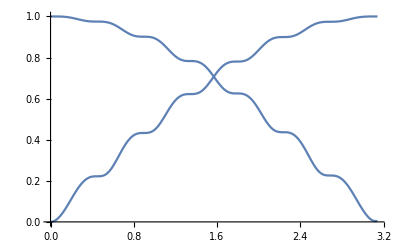

-Graphics3D-

```mathematica
Plot[ Abs@ sol[t], {t,0,Pi } ]

adiabaticgate = Graphics3D[ {
BlochSphereGraphics,
 Append[ TrajectorySettings,  TrajectoryFromFunction[ solThreeVecFun, trajectResolution ] ]
}, BlochSphereOptionsYZ ]
```

```mathematica
Export["blochgate_adiab_vec.pdf",GraphicsRow[{adiabaticgate},ImageSize->500]]
```

blochgate_adiab_vec.pdf